```mathematica
FinerSymbols[s_]:=Block[{t},
If[ListQ[s]
,
t=Map[SymbolToSets,s];
t=Flatten[Map[FindFiner,t],1];
t=Map[SetsToSymbol,t];
DeleteDuplicates[t]
,
Map[SetsToSymbol,FindFiner[SymbolToSets[s]]]
]
]
```

```mathematica
ShowGraph[g_]:=g->With[{f=FindFullFormula[g]},
Labeled[Graph[FormulaGraphReverse2[f],ImageSize->500],f]]
```

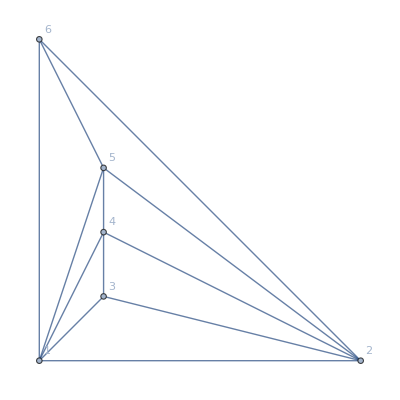
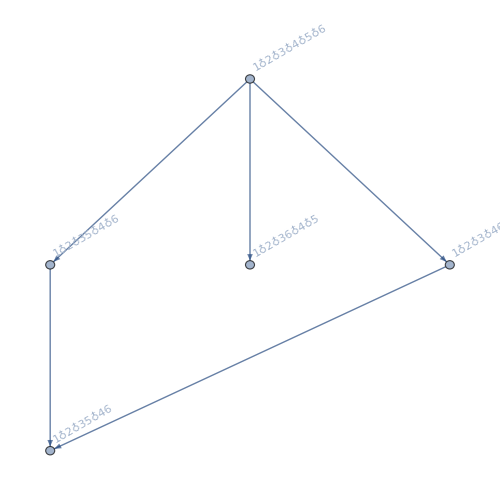
-Graphics-→-Graphics-{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46}

```mathematica
ShowGraph[MinimalGraph[5]]
```

```mathematica
Map[SetsToSymbol,FindFiner[SymbolToSets[v1x2x35x46]]]
```

{v1x2x3x46x5,v1x2x35x4x6}

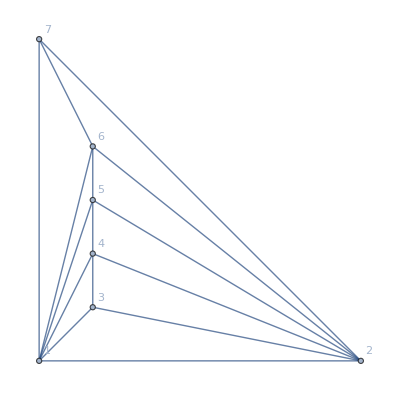
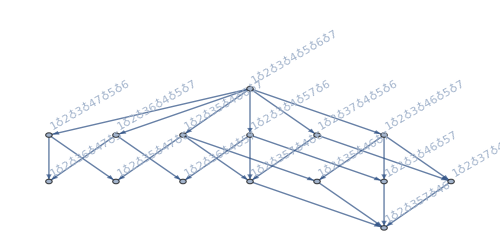
-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x57x6,v1x2x3x47x5x6,v1x2x3x46x5x7,v1x2x3x46x57,v1x2x37x4x5x6,v1x2x37x46x5,v1x2x36x4x5x7,v1x2x36x4x57,v1x2x36x47x5,v1x2x35x4x6x7,v1x2x357x4x6,v1x2x35x47x6,v1x2x35x46x7,v1x2x357x46}

```mathematica
ShowGraph[MinimalGraph[6]]
```

```mathematica
FinerSymbols[v1x2x357x46]
```

{v1x2x3x46x57,v1x2x35x46x7,v1x2x37x46x5,v1x2x357x4x6}

```mathematica
FinerSymbols[{v1x2x3x46x57,v1x2x35x46x7}]
```

{{{1},{2},{3},{4},{5,7},{6}},{{1},{2},{3},{4,6},{5},{7}},{{1},{2},{3},{4,6},{5},{7}},{{1},{2},{3,5},{4},{6},{7}}}

{v1x2x3x4x57x6,v1x2x3x46x5x7,v1x2x3x46x5x7,v1x2x35x4x6x7}

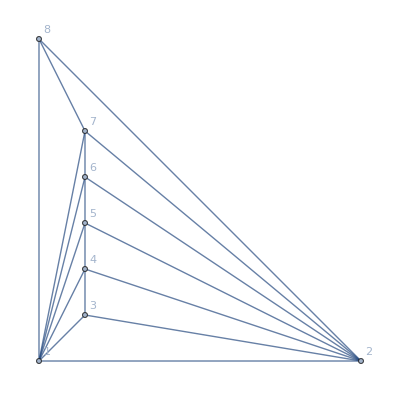
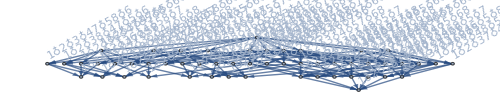
-Graphics-→-Graphics-{v1x2x3x4x5x6x7x8,v1x2x3x4x5x68x7,v1x2x3x4x58x6x7,v1x2x3x4x57x6x8,v1x2x3x4x57x68,v1x2x3x48x5x6x7,v1x2x3x48x57x6,v1x2x3x47x5x6x8,v1x2x3x47x5x68,v1x2x3x47x58x6,v1x2x3x46x5x7x8,v1x2x3x468x5x7,v1x2x3x46x58x7,v1x2x3x46x57x8,v1x2x3x468x57,v1x2x38x4x5x6x7,v1x2x38x4x57x6,v1x2x38x47x5x6,v1x2x38x46x5x7,v1x2x38x46x57,v1x2x37x4x5x6x8,v1x2x37x4x5x68,v1x2x37x4x58x6,v1x2x37x48x5x6,v1x2x37x46x5x8,v1x2x37x468x5,v1x2x37x46x58,v1x2x36x4x5x7x8,v1x2x368x4x5x7,v1x2x36x4x58x7,v1x2x36x4x57x8,v1x2x368x4x57,v1x2x36x48x5x7,v1x2x36x48x57,v1x2x36x47x5x8,v1x2x368x47x5,v1x2x36x47x58,v1x2x35x4x6x7x8,v1x2x358x4x6x7,v1x2x357x4x6x8,v1x2x35x4x68x7,v1x2x357x4x68,v1x2x35x48x6x7,v1x2x357x48x6,v1x2x35x47x6x8,v1x2x358x47x6,v1x2x35x47x68,v1x2x35x46x7x8,v1x2x35x468x7,v1x2x358x46x7,v1x2x357x46x8,v1x2x357x468}

```mathematica
ShowGraph[MinimalGraph[7]]
```

```mathematica
Table[With[{f=FindFullFormula4[JacobsThalGraph[k]]},
Framed[f->Column[Sort[FinerSymbols[f]]]]
],{k,4,5}]//TableForm
```

{v1x257x34x68,v17x26x34x58,v17x25x34x68,v16x27x34x58,v16x257x34x8,v168x2x34x57,v168x27x34x5,v18x26x34x57,v168x257x3x4,v18x257x34x6,v168x25x34x7}→v168x25x3x4x7
v168x27x3x4x5
v168x2x34x5x7
v168x2x3x4x57
v16x257x3x4x8
v16x25x34x7x8
v16x27x34x5x8
v16x27x3x4x58
v16x2x34x57x8
v16x2x34x58x7
v17x25x34x6x8
v17x25x3x4x68
v17x26x34x5x8
v17x26x3x4x58
v17x2x34x58x6
v17x2x34x5x68
v18x257x3x4x6
v18x25x34x6x7
v18x26x34x5x7
v18x26x3x4x57
v18x27x34x5x6
v18x2x34x57x6
v1x257x34x6x8
v1x257x3x4x68
v1x25x34x68x7
v1x26x34x57x8
v1x26x34x58x7
v1x27x34x58x6
v1x27x34x5x68
v1x2x34x57x68
{v1x268x34x579,v18x26x34x579,v18x257x34x69,v17x268x34x59,v17x258x34x69,v168x2x34x579,v16x28x34x579,v168x27x34x59,v168x257x34x9,v16x258x34x79,v168x25x34x79,v169x28x34x57,v169x27x34x58,v179x268x34x5,v179x26x34x58,v19x268x34x57,v179x258x34x6,v169x258x34x7,v169x257x34x8,v19x257x34x68,v179x25x34x68}→v168x257x3x4x9
v168x25x34x7x9
v168x25x3x4x79
v168x27x34x5x9
v168x27x3x4x59
v168x2x34x57x9
v168x2x34x59x7
v168x2x34x5x79
v168x2x3x4x579
v169x257x3x4x8
v169x258x3x4x7
v169x25x34x7x8
v169x27x34x5x8
v169x27x3x4x58
v169x28x34x5x7
v169x28x3x4x57
v169x2x34x57x8
v169x2x34x58x7
v16x257x34x8x9
v16x258x34x7x9
v16x258x3x4x79
v16x25x34x79x8
v16x27x34x58x9
v16x27x34x59x8
v16x28x34x57x9
v16x28x34x59x7
v16x28x34x5x79
v16x28x3x4x579
v16x2x34x579x8
v16x2x34x58x79
v179x258x3x4x6
v179x25x34x6x8
v179x25x3x4x68
v179x268x3x4x5
v179x26x34x5x8
v179x26x3x4x58
v179x28x34x5x6
v179x2x34x58x6
v179x2x34x5x68
v17x258x34x6x9
v17x258x3x4x69
v17x25x34x68x9
v17x25x34x69x8
v17x268x34x5x9
v17x268x3x4x59
v17x26x34x58x9
v17x26x34x59x8
v17x28x34x59x6
v17x28x34x5x69
v17x2x34x58x69
v17x2x34x59x68
v18x257x34x6x9
v18x257x3x4x69
v18x25x34x69x7
v18x25x34x6x79
v18x26x34x57x9
v18x26x34x59x7
v18x26x34x5x79
v18x26x3x4x579
v18x27x34x59x6
v18x27x34x5x69
v18x2x34x579x6
v18x2x34x57x69
v19x257x34x6x8
v19x257x3x4x68
v19x258x34x6x7
v19x25x34x68x7
v19x268x34x5x7
v19x268x3x4x57
v19x26x34x57x8
v19x26x34x58x7
v19x27x34x58x6
v19x27x34x5x68
v19x28x34x57x6
v19x2x34x57x68
v1x257x34x68x9
v1x257x34x69x8
v1x258x34x69x7
v1x258x34x6x79
v1x25x34x68x79
v1x268x34x57x9
v1x268x34x59x7
v1x268x34x5x79
v1x268x3x4x579
v1x26x34x579x8
v1x26x34x58x79
v1x27x34x58x69
v1x27x34x59x68
v1x28x34x579x6
v1x28x34x57x69
v1x2x34x579x68

```mathematica
Table[Length[FinerSymbols[First[FindFullFormula4[MinimalGraph2[k]]]]],{k,3,14}]
```

{0,1,2,3,4,9,8,15,14,22,20,28}